```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","ret/std"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Tue 1 Aug 2017

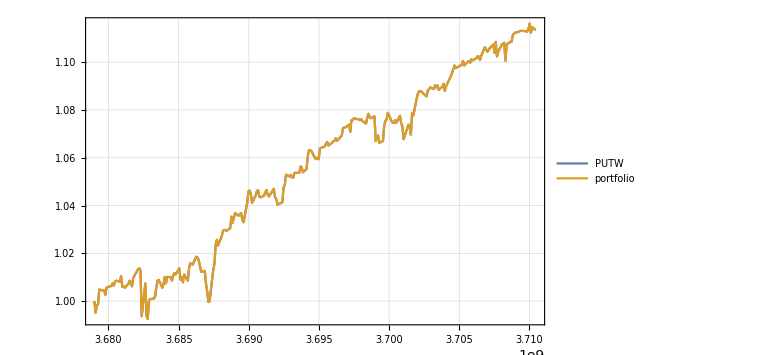
{-Graphics-,return | 1.11345
std | 0.0368974
ret/std | 30.1768}

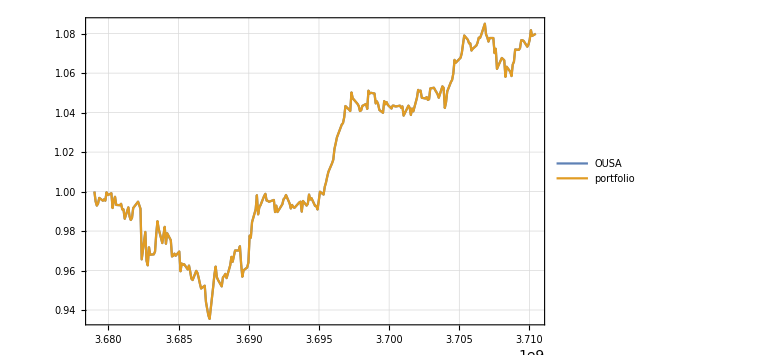
{-Graphics-,return | 1.07994
std | 0.0412397
ret/std | 26.1869}

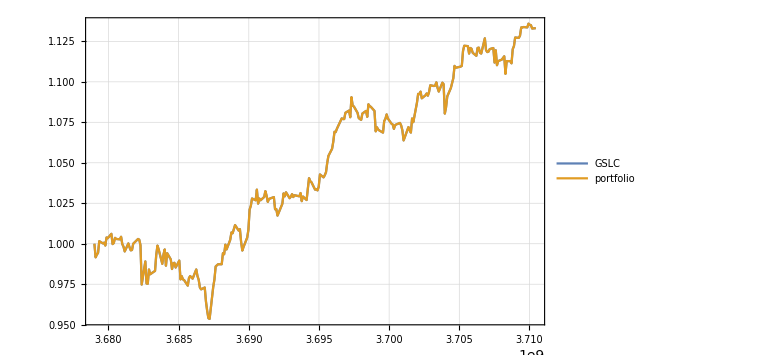
{-Graphics-,return | 1.13315
std | 0.0513064
ret/std | 22.086}

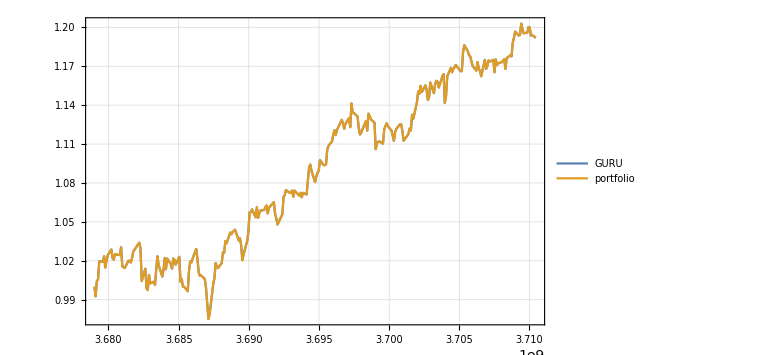
{-Graphics-,return | 1.19189
std | 0.0645721
ret/std | 18.4582}

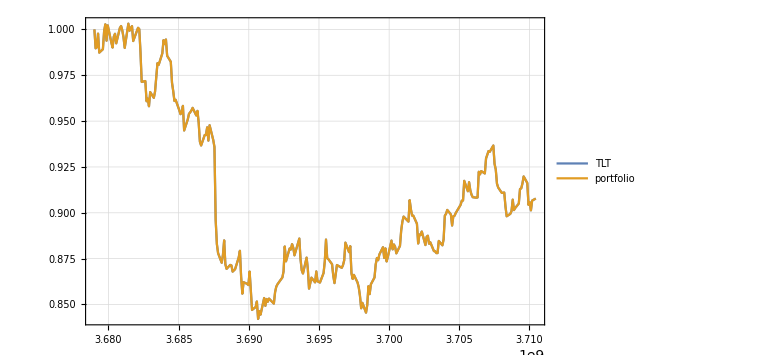
{-Graphics-,return | 0.907765
std | 0.0467344
ret/std | 19.4239}

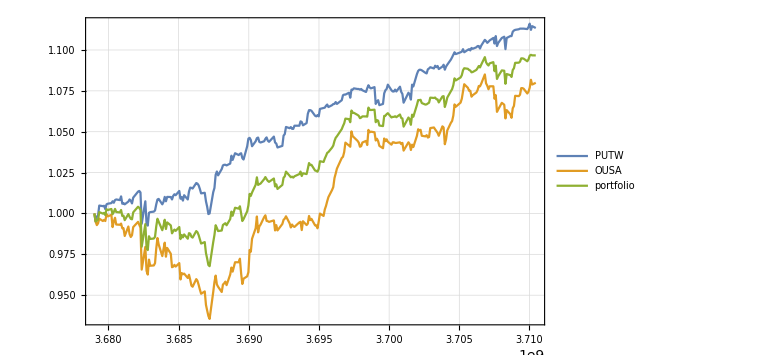
{-Graphics-,return | 1.09669
std | 0.0381501
ret/std | 28.7468}

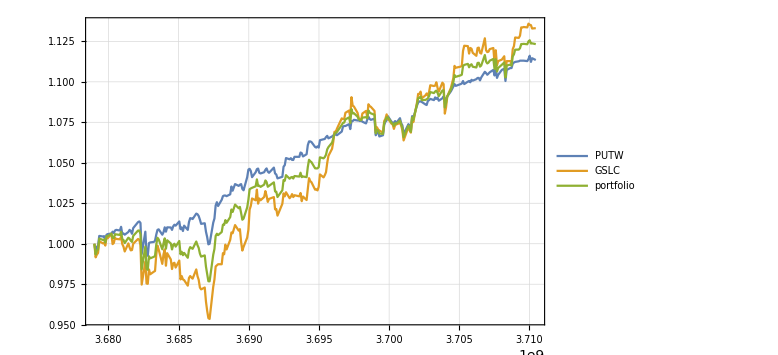
{-Graphics-,return | 1.1233
std | 0.0438032
ret/std | 25.6442}

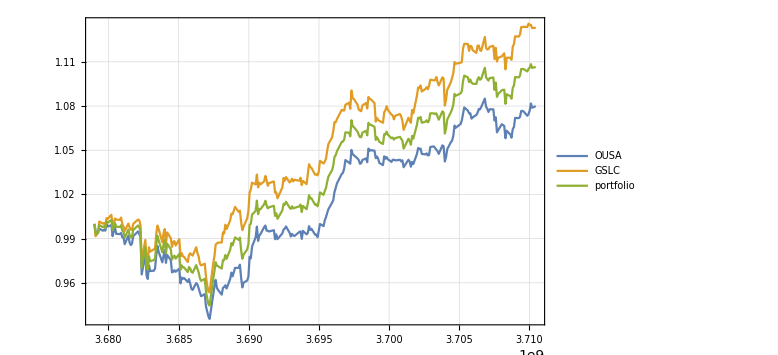
{-Graphics-,return | 1.10655
std | 0.0459921
ret/std | 24.0595}

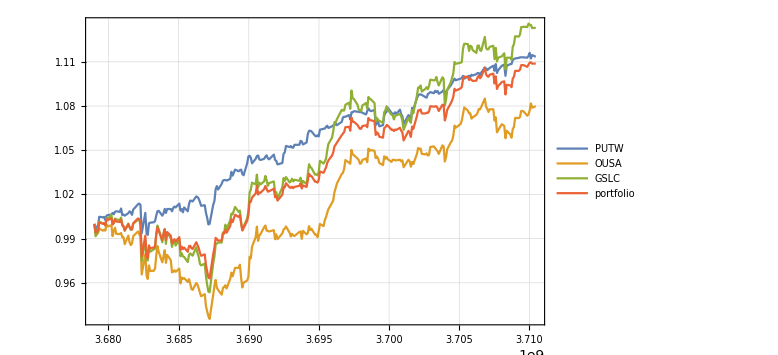
{-Graphics-,return | 1.10885
std | 0.0425091
ret/std | 26.0849}

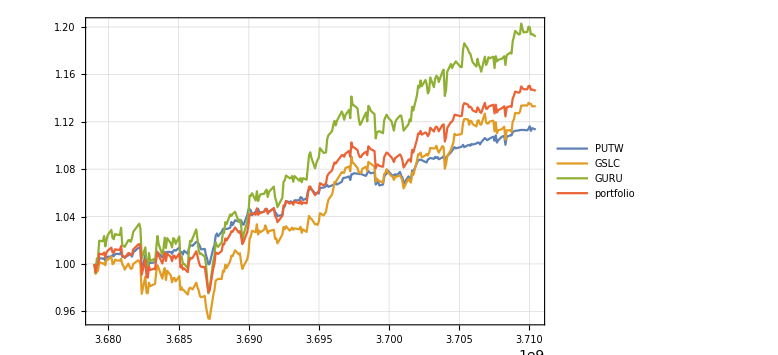
{-Graphics-,return | 1.14616
std | 0.0506749
ret/std | 22.6179}

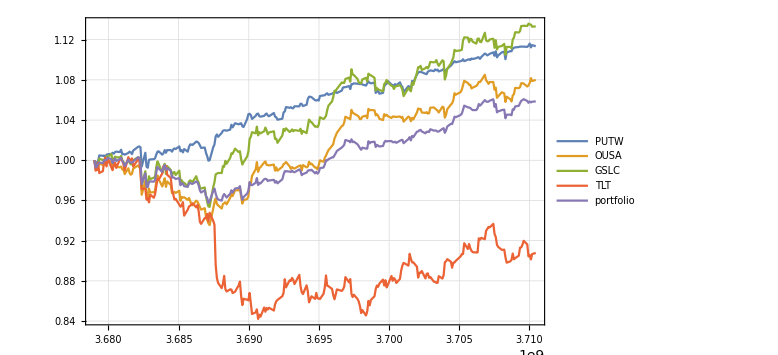
{-Graphics-,return | 1.05858
std | 0.0290289
ret/std | 36.4663}

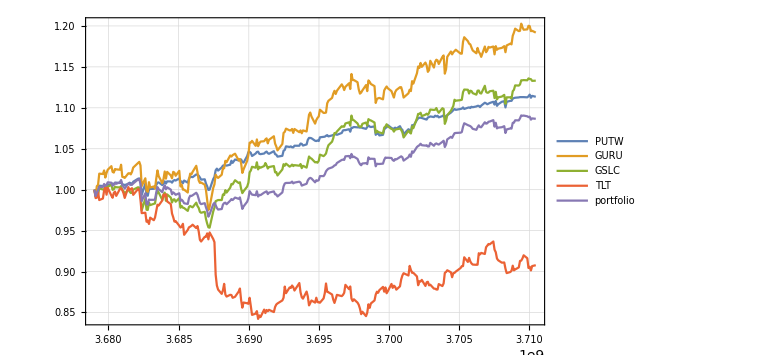
{-Graphics-,return | 1.08656
std | 0.0341392
ret/std | 31.8274}

```mathematica
PortfolioChart[{"PUTW"},start1,end]
PortfolioChart[{"OUSA"},start1,end]
PortfolioChart[{"GSLC"},start1,end]
PortfolioChart[{"GURU"},start1,end]
PortfolioChart[{"TLT"},start1,end]
PortfolioChart[{"PUTW","OUSA"},start1,end]
PortfolioChart[{"PUTW","GSLC"},start1,end]
PortfolioChart[{"OUSA","GSLC"},start1,end]
PortfolioChart[{"PUTW","OUSA","GSLC"},start1,end]
PortfolioChart[{"PUTW","GSLC","GURU"},start1,end]
PortfolioChart[{"PUTW","OUSA","GSLC","TLT"},start1,end]
PortfolioChart[{"PUTW","GURU","GSLC","TLT"},start1,end]
```

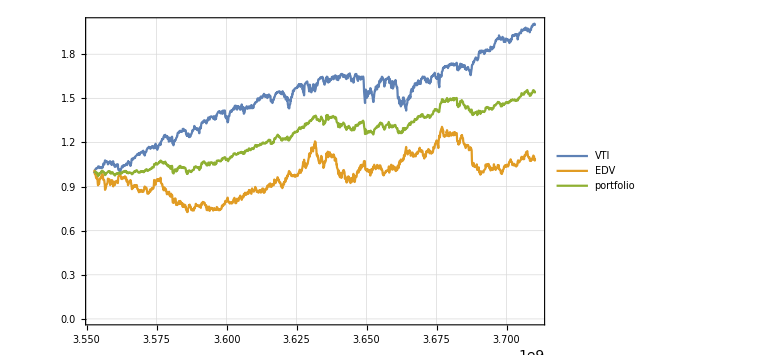
{-Graphics-,return | 1.54315
std | 0.173643
ret/std | 8.88694}

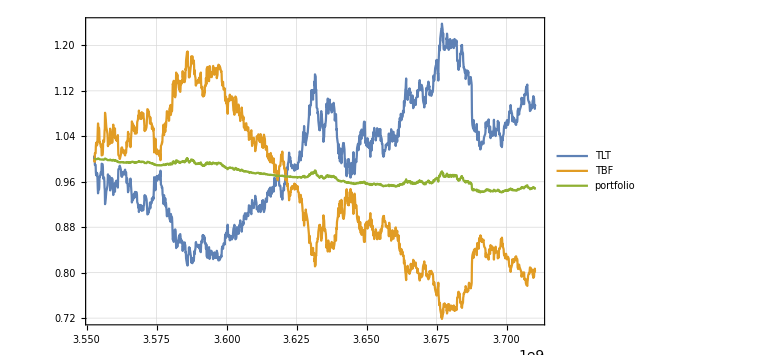
{-Graphics-,return | 0.948926
std | 0.0175634
ret/std | 54.0287}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

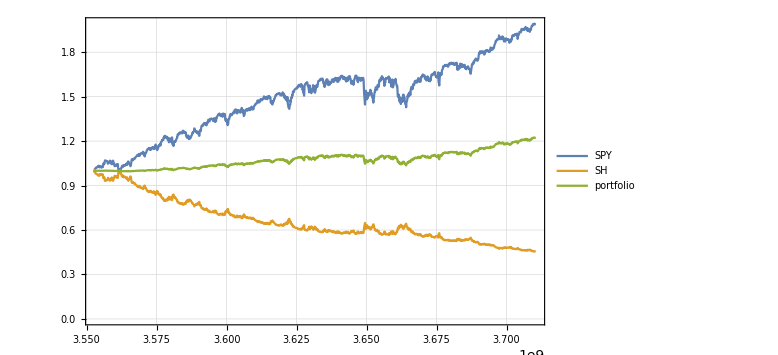
{-Graphics-,return | 1.22199
std | 0.0573465
ret/std | 21.3088}

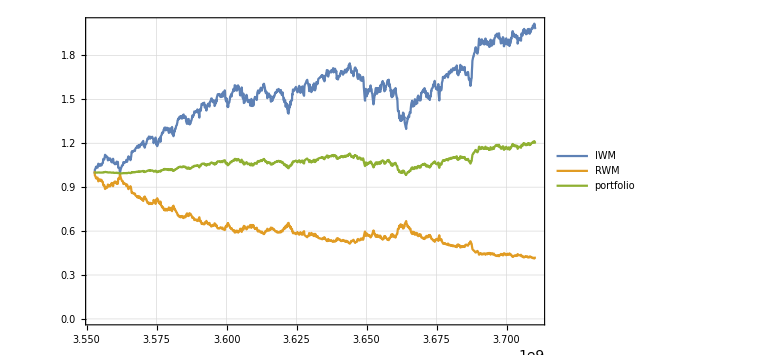
{-Graphics-,return | 1.2008
std | 0.0534611
ret/std | 22.4612}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

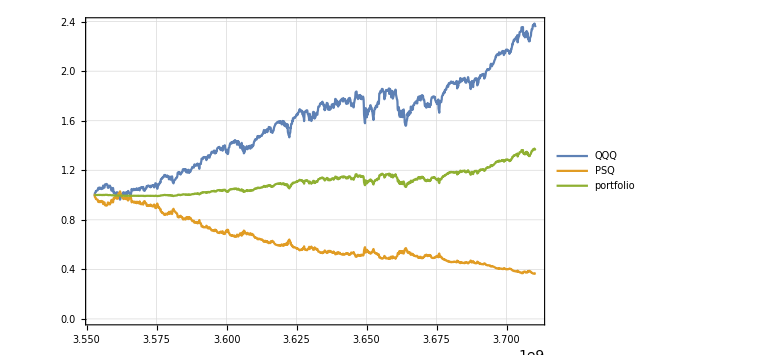
{-Graphics-,return | 1.36286
std | 0.0942428
ret/std | 14.4611}

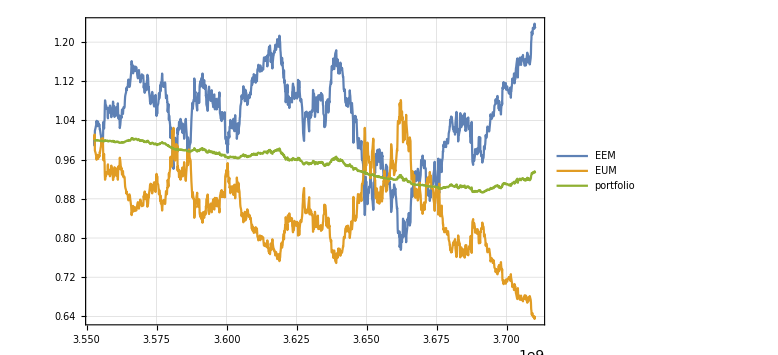
{-Graphics-,return | 0.935088
std | 0.0340253
ret/std | 27.4821}

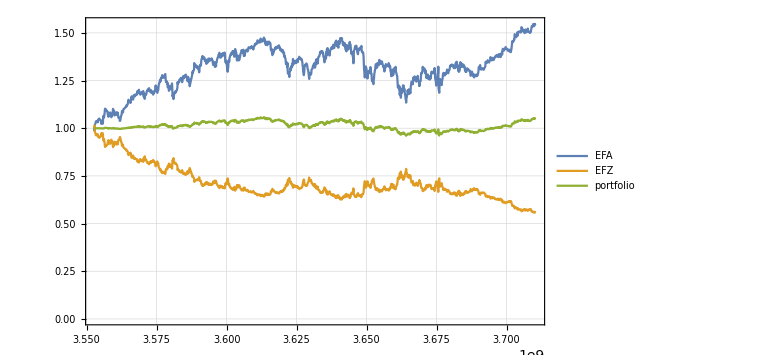
{-Graphics-,return | 1.05284
std | 0.0219055
ret/std | 48.0629}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

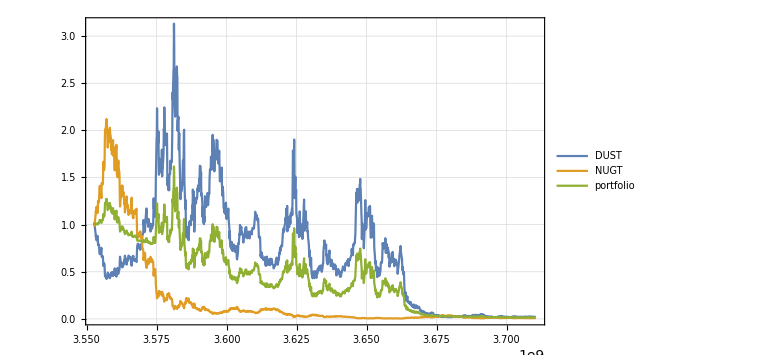
{-Graphics-,return | 0.0149596
std | 0.36137
ret/std | 0.0413969}

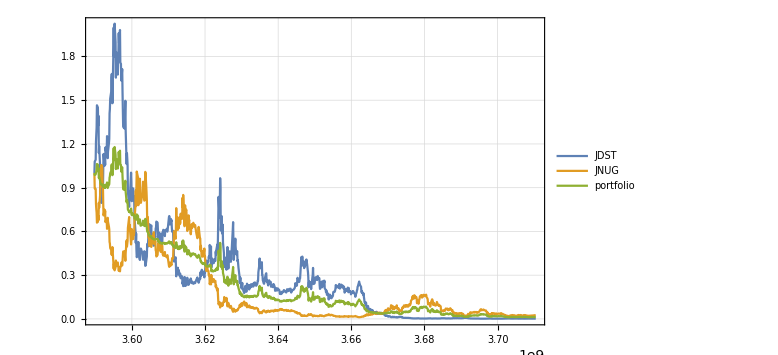
{-Graphics-,return | 0.0132286
std | 0.283547
ret/std | 0.046654}

```mathematica
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```